Задание 2.3 .5

-Graphics-
-Graphics-

Определим метод простой итерации

```mathematica
SimpleIteration[ϕ_,x0_,q_,epselon_]:=(n=1;
x1=x0;
x2=ϕ[x1];
While[Abs[x2-x1]≥(1-q)/q*epselon,{x1=x2;
x2=ϕ[x1];
n++;}];
Return[{x2//N,q,n}];);
```

Данные задачи

```mathematica
ϵ=10^-5;
f[x_]:=x-E^(-x^2);
```

Определим отрезок локализации

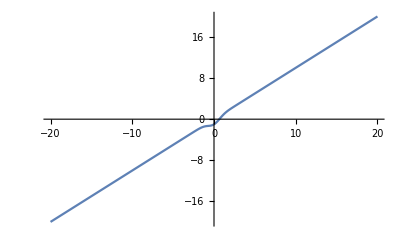

```mathematica
Plot[f[x],{x,-20,20}]
```

Возьмем отрезок локализации как[0.6; 0.7]

```mathematica
A=0.6;B=0.7;
```

Найдем константы m и M

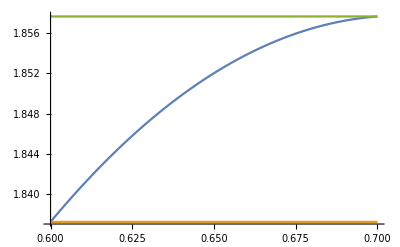

```mathematica
F [x_]=D[f[x],x];
Plot[{F[x],F[A],F[B]},{x,A,B}]
m = F[A]; M = F[B];
```

Определим функцию ϕ,значение q и начальное приблежение

```mathematica
ϕ[x_]:=x-2/(M+m)*f[x]
q=(M-m)/(M+m);
X=(A+B)/2;
```

Применим SimpleIteration

```mathematica
Print["{x,q,n} = ",SimpleIteration[ϕ,X,q,ϵ]]
```

{x,q,n} = {0.652919,0.00553883,2}

Для b) возьмем такую функцию x = γ (x), чтобы метод простой итерации стал методом Ньютона, а q = Q = max[γ’[x]]

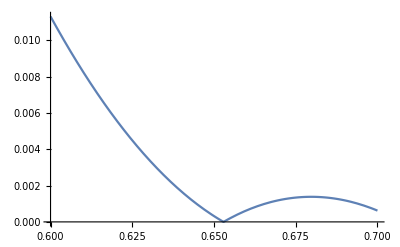

```mathematica
γ[x_]=x-f[x]/D[f[x],x];
Γ[x_]=D[γ[x],x];
Plot[Abs@Γ[x],{x,A,B}]
Q=Abs@Γ[A];
```

```mathematica
Print["{x,q,n} = ",SimpleIteration[γ,X,Q,ϵ]]
```

{x,q,n} = {0.652919,0.0113061,2}

Сравним все метода :

```mathematica
Print["A) {x,q,n} = ",SimpleIteration[ϕ,X,q,ϵ]]
Print["B) {x,q,n} = ",SimpleIteration[γ,X,Q,ϵ]]
Print["0) Встроеными функциями: x = ",FindRoot[f[x],{x,0}] ]
```

A) {x,q,n} = {0.652919,0.00553883,2}

B) {x,q,n} = {0.652919,0.0113061,2}

0) Встроеными функциями: x = {x→0.652919}